# Problemas - 2

Programación Estructurada

### Ejercicios 🐺

#### Ej 1

Encuentre una forma simple para Module[{a, i}, a=0; For[i=1, i≤1000, i++, a=i*(i+1)+a];a] usando Do.

```mathematica
a = 0;i = 0;
Do[
	a += i(i+1),
	{i,1000}
];
a
```

334334000

#### Ej 2

Encuentre una forma simple para Module[{i, j, a}, a={}; For[i=1, i≤10, i++, For[j=1, j≤10, j++, a=Join[a, {i, j}]]];a] usando Do.

```mathematica
Module[{i,j,a},a={};For[i=1,i≤10,i++,For[j=1,j≤10,j++,a=Join[a,{i,j}]]];a]
```

{1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,2,10,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,3,10,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,4,10,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,5,10,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,6,10,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,7,10,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,8,10,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,9,10,10,1,10,2,10,3,10,4,10,5,10,6,10,7,10,8,10,9,10,10}

```mathematica
i=0;j=0;a={};
Do[
Do[
	AppendTo[a,i];AppendTo[a,j],
	{j,10}
],
{i,10}
];
a
```

{1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,2,10,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,3,10,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,4,10,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,5,10,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,6,10,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,7,10,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,8,10,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,9,10,10,1,10,2,10,3,10,4,10,5,10,6,10,7,10,8,10,9,10,10}

#### Ej 3

Calcule una lista de números hasta el 100 que sean iguales a 1 mod 7 y mod 8 al mismo tiempo.

```mathematica
lis = {}
Do[
	If[IntegerQ[(i-1)/7] && IntegerQ[i/8] ,AppendTo[lis,i]],
	{i,1,100}
];
lis
```

{}

{8,64}

#### Ej 4

Haga un gráfico de arreglo de 50×50 en el cual un cuadrado en la posición i, j es negra si Mod[i, j]==0.

```mathematica
ArrayPlot[Table[If[Mod[i,j]==0,1,0],{i,1,50},{j,1,50}]]
```

-Graphics-

#### Ej 5

Dentro de un módulo, sea r = Range[10], realice un gráfico de lista de r unido con r invertido, unido con r y nuevamente con r invertido.

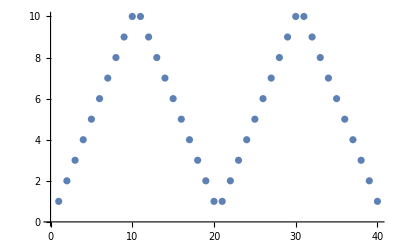

```mathematica
func[]:=Module[{r= Range[10],ri = Range[10,1,-1],l={}},AppendTo[l,{r,ri,r,ri}];ListPlot[Flatten[l]]]
func[]
```

#### Ej 6

Encuentre palabras en WordList[ ] cuyas tres primeras letras son las mismas que sus últimas letras leídas hacia atrás pero de modo que la palabra completa no sea un palíndromo.

```mathematica
lista = WordList[]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,40099,zoning,zoo,zoological,zoologist,zoology,zoom,zoophyte,zounds,zucchini,zwieback,zydeco,zygote,zygotic,zymurgy}
 |  |  |  |

```mathematica
lista = Characters[lista]
```

{{a},{a,a,h},{a,a,r,d,v,a,r,k},{a,b,a,c,k},{a,b,a,c,u,s},{a,b,a,f,t},40116,{z,w,i,e,b,a,c,k},{z,y,d,e,c,o},{z,y,g,o,t,e},{z,y,g,o,t,i,c},{z,y,m,u,r,g,y}}
 |  |  |  |

```mathematica
pal1 = {"Hola","Coau"};
pal2 = Characters[pal1];
pal2[[1]][[-2]]
```

l

```mathematica
lis = {};
Do[
If[ Length[lista[[i]]] ≥ 3 && lista[[i]][[1]] == lista[[i]][[-1]] && lista[[i]][[2]] == lista[[i]][[-2]] && lista[[i]][[3]] == lista[[i]][[-3]] &&PalindromeQ[lista[[i]]],AppendTo[lis,StringJoin[lista[[i]]]]]
,{i,1,Length[lista]}
];
lis
```

{aha,bib,bob,boob,civic,dad,deed,dud,ere,eve,ewe,eye,gag,gig,huh,kayak,kook,level,ma'am,madam,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,poop,pop,pup,radar,refer,rotor,sis,tat,tenet,toot,tot,tut,wow}

### Problema 1

La secuencia de Fibonacci esta dada por: 1, 1, 2, 3, 5, 8, 13, 21,…, donde cada número es obtenido sumando los dos anteriores . Escribe una función que calcule el enésimo número de la secuencia de Fibonacci.

```mathematica
fact[n_]:=
Module[{a,b,c},
a=0;b=1;
Do[
c= b;b = a+b;a = c,
{n}
];
a
]
fact[7]
```

13

### Problema 2

Para dos números reales a y g las dos secuencias a_i y g_i, definidas como sigue , convergen a un límite común, denominado la media aritmética-geométrica.

a_0=a
g_0=g
a_(i+1)=(a_i+g_i)/2
g_(i+1)=√(a_i g_i)

Escribe una función AGM[a,g] para calcular este límite.

```mathematica
AGM[a_,g_]:=Module[{aux1=a,aux2=g,cont=0},
While[
Abs[aux1-aux2]>10^-10 && cont < 100,
	x = aux1; y = aux2;cont++;
	aux1 =N[ Mean[{x,y}]]; aux2= N[GeometricMean[{x,y}]];
];
Print[{aux1,aux2}]
]
AGM[4,10]
```

{6.65799,6.65799}

### Problema 3

Cambiar el algoritmo, visto en clase, para generar una permutación aleatoria  de un conjunto de datos , de modo que use Sow y Reap.

### Problema 4

Escribe un programa estructurado myTally[lista] que recibe una lista y devuelve el mismo resultado que Tally[lista].

```mathematica
Tally[{a,c,d,e,f,f,a,e}]
```

{{a,2},{c,1},{d,1},{e,2},{f,2}}

```mathematica
myTally[lista_] := Module
```

### Problema 5

Escribe un algoritmo estructurado que realice lo que mismo que el comando Pick

```mathematica
Pick[{A,B,C,D,E},{1,0,1,0,0},1]
```

{A,C}

```mathematica
funcion[a_,b_,c_]:=Module[{n},
n = Length[a];
lis = {};
Do[
	If[b[[i]]==c,AppendTo[lis,a[[i]]]],
	{i,1,n}
];
lis
]
funcion[{1,2,3,4,5},{1,0,1,0,0},1]
```

{1,3}

### Problema 6

Escribe un algoritmo estructurado que realice lo que mismo que el comando Nest

### Problema 7

Dado una lista de puntos en el plano, donde cada punto estas dado por un par de coordenadas {x,y}, escribe una función que determine cuál es la máxima distancia entre un par de puntos cualesquiera. Este valor es llamado el diámetro del conjunto.